```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]]
```

{{0.5,-16.3721,4.436},{0.75,-28.6714,12.936},{1,-44.4515,27.245},{1.5,-86.4495,79.22},{2,-142.363,173.925},{3,-295.93,558.493},{4,-505.15,1395.63},{6,-1090.55,6293.03},{8,-1898.55,23937.6},{10,-2929.17,85318.8}}

```mathematica
NormTF[core_?ArrayQ]:=Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^2/(4 (core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
];


WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(lam^2+2Bb-2 Hh)+Aa(-4(1/4)lam^2-2Bb+2Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)-TwoMyOverHBsq Ee)  SphericalBesselJ[0,I b1 r rp]
-4 a1 b1 r rp I Sqrt[3]^-1 SphericalBesselJ[1,I b1 r rp])
+zeta2 SphericalBesselJ[0,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+zeta3 SphericalBesselJ[0,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];

NormTF[{{-0.8980539125325929,9.858578},{-0.36208149062791306,2.607968},{-0.22631177434298616,0.618807},{-0.10573147650203236,0.108375}}]
```

0.405726

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_,LECc_]:=Module[{locall=l},

energ=0.01(*Range[0.0001,0.25,0.025]*);
LECd=0.0;

momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

```mathematica
dimerCore421={{-0.07319267680072254,0.05278247284807325},{-0.19191435678365207,0.2876133832274892},{-0.4483081958567124,1.1845268166888943},{-0.8699606159193424,5.696212814971323}};
dimerCore321={{0.1670350700426946,0.08153236423287158},{0.5190030918916717,0.652331092635837},{0.8382929535566411,3.3620395216118695}};
dimerCore80778={{0.12168505395239915,0.14210165496265503},{0.38161492699467175,1.8870346920713708},{0.9162765931417507,15.005656345800315}};
dimerCore8081={{0.12068342146732587,0.15729406167437787},{0.3695980467895534,1.7920203455098438},{0.9213212228057525,15.566187630799618}};
```

{35,60,85,110,135}

λ = 8   C_0(λ) = -1898.55     R_max = 8     #(grid points) = 35

λ = 8   C_0(λ) = -1898.55     R_max = 8     #(grid points) = 60

λ = 8   C_0(λ) = -1898.55     R_max = 8     #(grid points) = 85

λ = 8   C_0(λ) = -1898.55     R_max = 8     #(grid points) = 110

λ = 8   C_0(λ) = -1898.55     R_max = 8     #(grid points) = 135

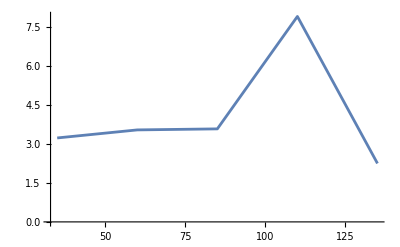

```mathematica
dimerCore=dimerCore8081;
lamd=8;
scaleFactor=1.0;
LECc =scaleFactor Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]];
rMa=8;

nGrdi=4;
nGrdiMi=35;
nGrdiMa=100+nGrdiMi;
nGr=Range[nGrdiMi,nGrdiMa,Quotient[nGrdiMa-nGrdiMi,nGrdi]]
results={};
SetSharedVariable[results,resultsPhases];

ParallelDo[

Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd];
tmp=GetERE[lamd,rMa,nGrd,dimerCore,LECc];
AppendTo[results,tmp];
,{nGrd,nGr}]
ListPlot[Transpose[{nGr,results}],Joined->True]
```

λ = 4: B(2) = 2.14 , a_dd≈7 , R_max=8

```mathematica
Subscript[a, ff]=hbar/√(Mm 2.14);
7/Subscript[a, ff]
```

1.59008

λ = 3: B(2) = 2.06 , a_dd≈22 , R_max=8

```mathematica
Subscript[a, ff]=hbar/√(Mm 2.06);
22/Subscript[a, ff]
```

4.90309

λ = 8: B(2) = 0.778 , a_dd≈3.4  , R_max=8

```mathematica
Subscript[a, ff]=hbar/√(Mm 0.778);
3.4/Subscript[a, ff]
```

0.465674

λ = 8: B(2) = 0.81 , a_dd≈  , R_max=8

```mathematica
Subscript[a, ff]=hbar/√(Mm 0.81);
/Subscript[a, ff]
```

0.465674

```mathematica
energ=0.01;
nR=80;
rMi=0.01;
rMa=10;
rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];

potnoloc3d={};
potnoloc3d=Flatten[ParallelTable[{rR[[i]],rR[[j]],WnolocTF[rR[[i]],rR[[j]],energ,lamd,LECc,0.0,dimerCore[[1]][[2]],dimerCore[[1]][[2]],dimerCore[[1]][[2]],dimerCore[[1]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
ListDensityPlot[Re[potnoloc3d],Mesh->All,PlotRange->All]
```

-Graphics-